## LOAD OPTEX

```mathematica
SetDirectory[NotebookDirectory[]];
<<OptEx.m
<<CustomPlotFunctions.m
```

OptEx-1.0

Sunando K. Patra
 Bangabasi Evening College, Univ. of Calcutta
 West Bengal, India

If you are using OptEx for the first time, try running ' OptExHelp[ ]; '.

### Replace Lists

These lists define the relations amongst the SM couplings, masses etc.

```mathematica
lstcoupling={gS->√(4 π alphas),gW->(2 √(π alpha))/s,gY->(2 √(π alpha))/c,yud->(√2 mb)/v,yue->(√2 mtau)/v,yuu->(√2 mt)/v,l-> 1/(√(√2 gf)),λH-> mh^2/(2 v^2)};
lstexp={v->1/(√(√2 gf)),s->√(1/2-1/2 √(1-(4 π alpha)/(√2 gf mz^2))),c->√(1/2+1/2 √(1-(4 π alpha)/(√2 gf mz^2)))};
lstval={gf->0.000011663787000000001,alpha->7.2973525664*10^-3,mb-> 4.18,mtau-> 1.77};
rplst=lstcoupling/.lstexp/.lstval;
replstwc=<|"q1Hl[1,1]"->"q1Hl11","q1Hq[1,1]"->"q1Hq11","q3Hl[1,1]"->"q3Hl11","q3Hq[1,1]"->"q3Hq11","qdH[1,1]"->"qdH11","qeH[1,1]"->"qeH11","qH"->"qH","qHB"->"qHB","qHbox"->"qHbox","qHD"->"qHD","qHd[1,1]"->"qHd11","qHe[1,1]"->"qHe11","qHG"->"qHG","qHu[1,1]"->"qHu11","qHW"->"qHW","qHWB"->"qHWB","qll[1,1,1,1]"->"qll1111","quH[1,1]"->"quH11"|>;
```

## Constructing allowed Parameter Space Plots (2D Posteriors)

### Model : 𝒮

Load the matching results:

```mathematica
matchwcS=Import[FileNameJoin[{NotebookDirectory[],"wcs","S_match.m"}]];
```

Load Wilson coefficient fit result (model parameter independent):

```mathematica
fitwcS=loadRun["Swc"];
```

Load Wilson coefficient fit result (model parameter dependent):

```mathematica
fitwcparamS=loadRun["Sparam"];
```

```mathematica
stringlstwc=Module[{wc,wc1,lst1,lst2},
wc=matchwcS[[2]][[All,1]];
wc1=StringDelete[StringReplace[#,((#-> "m")&/@{"[",",","]"})],"m"]&/@wc;
lst1=StringDelete[StringDrop[#,1],DigitCharacter]&/@wc1;
lst2=(Subscript[Q,ToExpression[#]]&/@lst1)/.{Subscript[Q, ll1111]-> Subscript[Q, ll]};
AssociationThread[Join[ToExpression/@wc1,{mz,alphas,mh,halpha,mt}],Join[(ToString[#,FormatType-> StandardForm]&/@lst2)/.{"\!\(\*SubscriptBox[\"Q\", \"Hbox\"]\)"-> "Q_(H □)"},{"m_z","α_s","m_H","Δα_had^(5)(m_Z^2)","m_t"}]]];
```

We show 2D posterior derived from Wilson coefficients (parameter independent) fit:

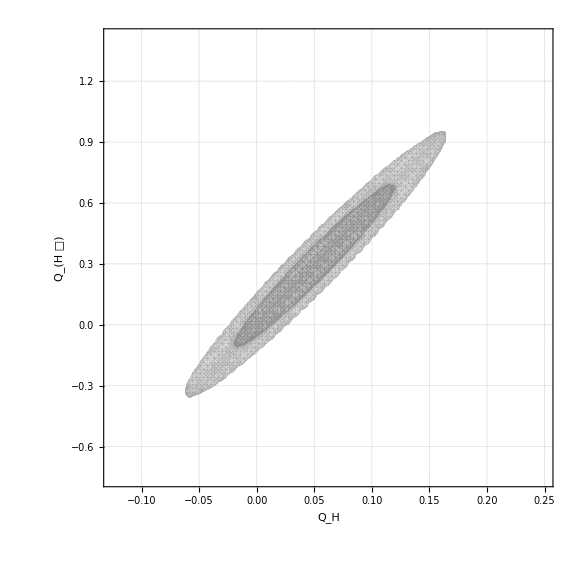

```mathematica
wcplot=With[{mcres=fitwcS,parinds={1,2}},
custompost2D[mcres,parinds,color->Gray,siglst->{1,2},range->All,xyLabel->Evaluate[mcres["Parameters"][[parinds]]/.stringlstwc],points->300,contourStyle->None,contourShading->"Default",PerformanceGoal->"Quality",PlotPoints->60,GridLines->Automatic,AspectRatio->1]
]
```

We show 2D posterior derived from Wilson coefficients (parameter dependent) fit:

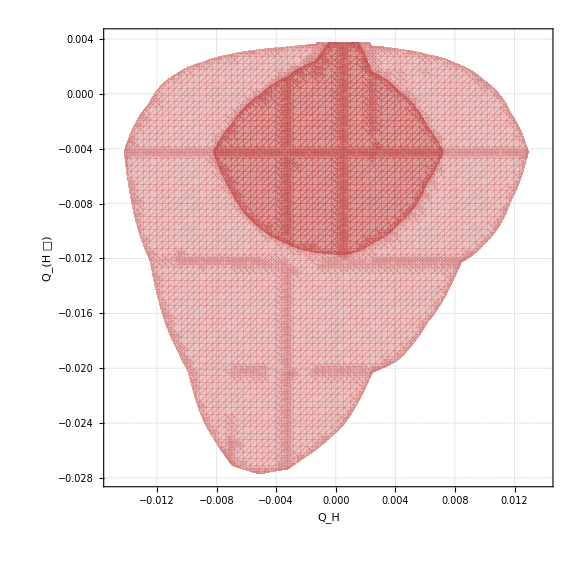

```mathematica
wcparamplot=wcPlotFromModel[fitwcparamS,matchwcS,{m->1000.,m𝒮->1000.,λ𝒮->0,μ𝒮->0},{qH,qHbox},Red,{1,2},{{-0.015,0.014},{-0.028,0.0041}}]
```

### For other models:

All MCMC Runs for model dependent and independent fits are available in the folder: OptExMCRuns
All SMEFT matching results are available in the folder: wcs

In order to reproduce the 2D posterior plots for other models, users are required to repeat the above mentioned workflow in similar manner using the files provided in ‘OptExMCRuns’ and ‘wcs’ .